```mathematica
DiscreteWaveletTransform[{56,40,8,24,48,48,40,16}]
```

DiscreteWaveletData[<<DWT>>, <3>, {8}]

```mathematica
WaveletScalogram[%1]
```

-Graphics-

```mathematica
Normal[%]
```

{{0}→{67.8823,22.6274,67.8823,39.598},{1}→{11.3137,-11.3137,0.,16.9706},{0,0}→{64.,76.},{0,1}→{32.,20.},{0,0,0}→{98.9949},{0,0,1}→{-8.48528}}

```mathematica
TableForm[Apply[List,%2,{1}]]
```

0 | 67.8823
22.6274
67.8823
39.598
1 | 11.3137
-11.3137
0.
16.9706
0
0 | 64.
76.
0
1 | 32.
20.
0
0
0 | 98.9949
0
0
1 | -8.48528

```mathematica
a=Audio["ExampleData/rule30.wav"]
```

```mathematica
dwd=DiscreteWaveletTransform[a,Automatic,3]
```

DiscreteWaveletData[<<DWT>>, <3>, {79380}]

```mathematica
dwd[All,"Audio"]
```

{{0}→,{1}→,{0,0}→,{0,1}→,{0,0,0}→,{0,0,1}→}

```mathematica
dwd=DiscreteWaveletTransform[-Graphics-,Automatic,2]
```

DiscreteWaveletData[<<DWT>>, <2>, {160, 160}]

```mathematica
dwd[All,"Image"]
```

{{0}→-Graphics-,{1}→-Graphics-,{2}→-Graphics-,{3}→-Graphics-,{0,0}→-Graphics-,{0,1}→-Graphics-,{0,2}→-Graphics-,{0,3}→-Graphics-}

```mathematica
InverseWaveletTransform[dwd]
```

-Graphics-

```mathematica
dwd=DiscreteWaveletTransform[Range[8]];
```

```mathematica
Normal[dwd]
```

{{0}→{2.12132,4.94975,7.77817,10.6066},{1}→{-0.707107,-0.707107,-0.707107,-0.707107},{0,0}→{5.,13.},{0,1}→{-2.,-2.},{0,0,0}→{12.7279},{0,0,1}→{-5.65685}}

```mathematica
DiscreteWaveletTransform[Range[8]]
```

DiscreteWaveletData[<<DWT>>, <3>, {8}]

```mathematica
WaveletScalogram[%13]
```

-Graphics-

```mathematica
dwd=DiscreteWaveletTransform[Table[Sin[x^2],{x,0,10,0.2}],Automatic,4]
```

DiscreteWaveletData[<<DWT>>, <4>, {51}]

```mathematica
First/@dwd[Automatic]
```

{{1},{0,1},{0,0,1},{0,0,0,1},{0,0,0,0}}

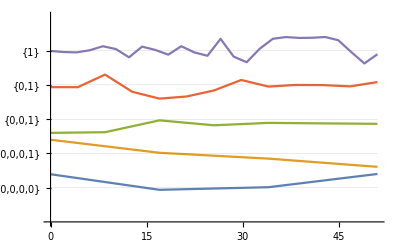

```mathematica
WaveletListPlot[dwd,Ticks->Full]
```

```mathematica
data=Table[Sin[x^2]+RandomReal[{-0.2,0.2}],{x,0,10,0.02}]
```

{0.0511336,0.079919,-0.0351801,-0.0792867,-0.0464217,-0.10628,0.209528,-0.152084,0.0350143,0.202927,0.155497,0.216618,-0.00561407,0.252552,0.139093,0.132692,0.0969561,-0.0845413,0.223263,0.208362,0.272827,0.311182,0.358912,0.230989,0.298569,0.412289,0.419802,0.386798,0.200297,0.489385,0.352738,0.226411,0.317167,0.29366,0.447541,0.340544,0.551833,0.324625,0.744056,0.410943,0.753905,0.563154,0.703722,0.848825,0.889149,0.776493,0.870346,0.61017,0.640651,0.657318,1.02667,1.01411,0.68786,0.990141,0.759833,1.02328,0.786514,0.906999,1.1617,1.17837,0.802382,0.996387,1.01068,1.07096,1.03478,1.05888,1.15088,1.16995,1.08931,1.00754,1.11225,0.813937,0.927742,0.836438,0.684502,0.584731,0.566228,0.599519,0.579674,0.435522,0.608113,0.649907,0.605173,0.379839,0.394134,0.258387,0.178444,0.0632184,-0.048128,0.0968399,-0.135468,-0.166272,-0.109496,-0.232452,-0.469698,-0.584838,-0.523796,-0.5453,-0.822819,-0.836427,-0.71131,-0.694993,-0.856421,-0.790674,-0.762695,-1.10475,-0.913533,-0.972285,-0.841147,-0.863994,-0.817546,-0.988804,-1.02297,-1.00736,-0.840853,-0.96588,-0.75394,-0.866904,-0.642156,-0.428767,-0.367613,-0.451093,-0.408287,-0.229247,-0.0768106,0.000324084,0.0449949,0.0669324,0.358799,0.269084,0.582906,0.596772,0.479197,0.618856,0.838847,0.954246,0.742028,0.933479,0.979375,0.962898,1.02997,0.826909,0.982656,0.953478,0.74896,0.944785,0.612025,0.623617,0.620504,0.455143,0.296729,0.280524,-0.000611397,0.225088,-0.182734,-0.00397631,-0.154995,-0.357293,-0.575206,-0.582187,-0.679147,-0.712509,-0.853501,-0.743865,-0.881432,-1.17024,-0.921316,-1.16567,-1.11576,-0.930284,-1.01487,-0.746251,-0.661068,-0.433668,-0.539074,-0.168234,-0.284638,-0.0359883,0.013046,0.139534,0.464581,0.506728,0.478548,0.716443,0.871432,0.763988,1.05835,1.06513,1.08783,0.813064,1.03759,0.850339,0.85903,0.755434,0.794059,0.650262,0.223196,0.14658,-0.0350255,-0.250906,-0.36992,-0.517727,-0.456632,-0.607726,-0.756521,-0.920079,-1.00107,-1.10125,-1.01025,-0.846617,-0.771639,-0.741139,-0.573341,-0.7648,-0.494159,-0.264134,-0.269195,-0.00831263,0.122012,0.494683,0.476707,0.442366,0.899642,0.904203,0.87127,1.17613,0.930835,0.993601,0.892624,0.966997,0.776853,0.621488,0.298965,0.338173,0.0100498,0.0435589,-0.144583,-0.27733,-0.649379,-0.723717,-0.689473,-1.09377,-1.03677,-1.17009,-0.95656,-0.898436,-0.998637,-0.836596,-0.520121,-0.22169,-0.313691,0.101416,0.218745,0.538498,0.647384,0.81909,0.857936,1.04447,0.827493,1.17892,0.745449,0.984244,0.529955,0.512938,0.242821,0.195612,-0.135438,-0.33672,-0.378806,-0.503742,-0.890399,-0.717958,-1.16372,-1.06672,-1.17323,-0.730632,-0.671614,-0.724164,-0.318617,-0.279068,0.0973747,0.076009,0.394773,0.726616,0.867646,0.971991,1.06564,0.858374,1.1374,0.859098,0.88135,0.769751,0.322207,0.322349,0.0153301,-0.223812,-0.465335,-0.553367,-0.893972,-0.836216,-0.885036,-0.955937,-1.05286,-0.791242,-0.746822,-0.533822,-0.172616,-0.0545936,0.382825,0.636385,0.818401,0.776156,1.09048,1.08262,0.873474,0.782591,0.692017,0.555172,0.312235,-0.0468184,-0.172566,-0.548923,-0.400704,-0.651831,-1.02096,-1.09518,-0.818685,-0.753342,-0.946952,-0.556606,-0.467883,-0.228213,0.246876,0.224121,0.600562,0.767113,0.804341,1.09188,1.16964,1.01085,0.930882,0.618588,0.486514,0.140152,-0.292128,-0.32183,-0.737874,-0.833569,-0.913575,-1.00136,-0.853759,-0.977513,-0.690148,-0.526277,-0.0405057,0.0162247,0.385365,0.702918,0.962322,0.950871,1.0223,0.90626,0.662599,0.768161,0.217504,-0.0214464,-0.0626603,-0.51067,-0.586828,-0.958482,-1.15677,-1.18388,-0.969175,-0.629859,-0.624953,-0.33467,-0.118587,0.486473,0.470091,0.810086,0.801863,0.918449,1.13059,0.663456,0.561223,0.556072,0.272938,-0.343218,-0.437732,-0.806011,-1.06993,-0.821247,-0.863357,-0.735283,-0.753402,-0.541211,-0.00552504,0.357204,0.58919,0.792926,0.801216,0.900005,1.09472,0.745753,0.58583,0.524612,0.185718,-0.222818,-0.532383,-0.659479,-0.77564,-0.842389,-0.92852,-0.7702,-0.681402,-0.355204,0.166977,0.590581,0.62463,1.06309,0.888828,1.00996,0.933689,0.591806,0.416677,-0.0868173,-0.27951,-0.570774,-0.894065,-0.843338,-0.947808,-0.887525,-0.518334,-0.576069,-0.23086,0.440279,0.755352,0.769838,0.809283,1.00065,0.879936,0.600419,0.461761,-0.102444,-0.233153,-0.689745,-0.916379,-1.06324,-1.15598,-0.776524,-0.721034,-0.384949,-0.0325189,0.372444,0.804816,0.725032,0.895743,0.941065,0.881445,0.501576,0.0735388,-0.186693,-0.492434,-0.687455,-1.08701,-0.890125,-0.769235,-0.780497,-0.486348,0.0810406,0.480047,0.771152,0.922752,1.04628,1.12751,0.91775,0.536225,0.243738,-0.0921449,-0.653139,-0.826309,-0.916304,-0.90713,-0.93825,-0.585157,-0.250391,0.401356,0.422293,0.745372,1.0797,0.875342,0.993871,0.598139,0.301238,-0.3323,-0.403203,-0.930922,-1.03064,-0.799719,-0.921103,-0.450945}

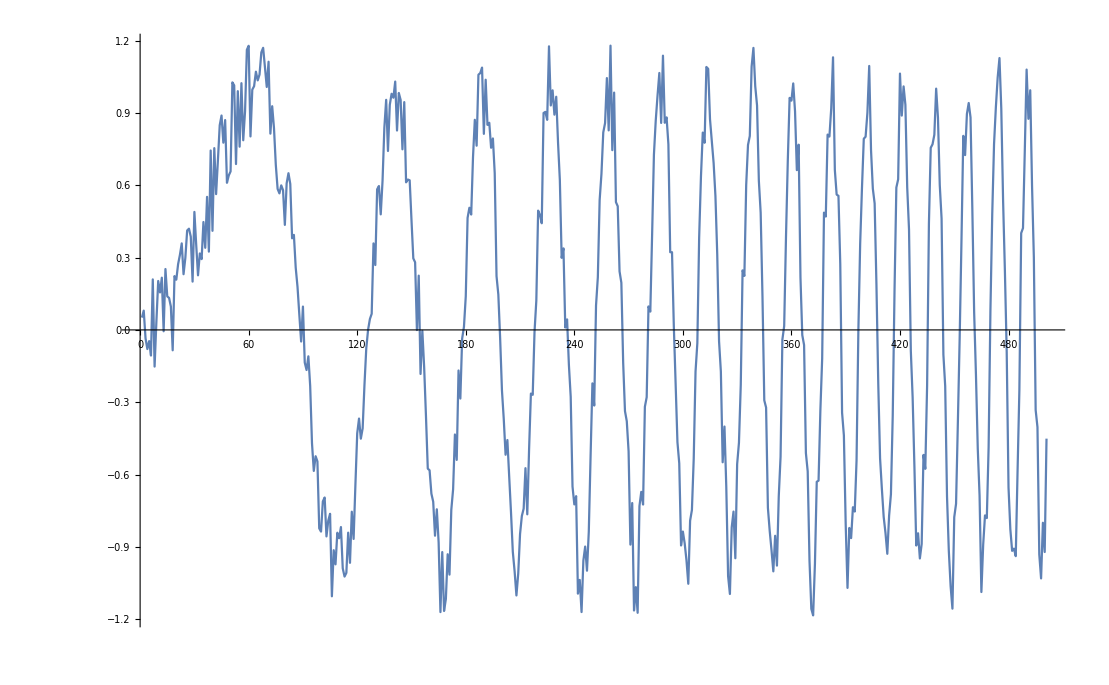

```mathematica
ListLinePlot[data]
```

```mathematica
dwt1=DiscreteWaveletTransform[data,DaubechiesWavelet[4],3];
```

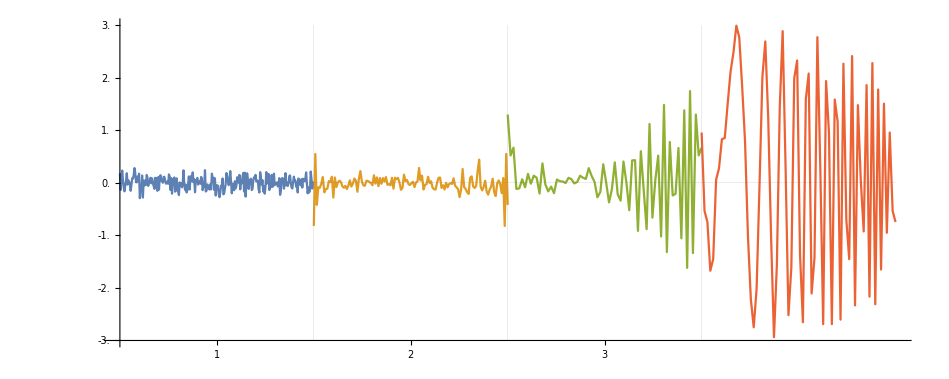

```mathematica
WaveletListPlot[dwt1,PlotLayout->"CommonYAxis"]
```

```mathematica
dwt2=DiscreteWaveletTransform[data,DaubechiesWavelet[4],4]
```

DiscreteWaveletData[<<DWT>>, <4>, {501}]

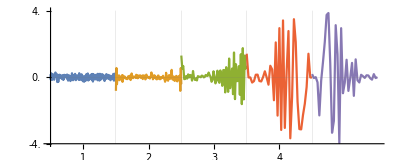

```mathematica
WaveletListPlot[dwt2,PlotLayout->"CommonYAxis"]
```

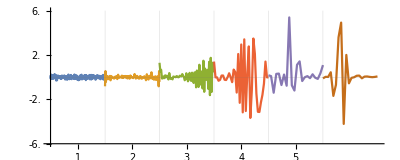

```mathematica
WaveletListPlot[DiscreteWaveletTransform[data,DaubechiesWavelet[4],5],PlotLayout->"CommonYAxis"]
```

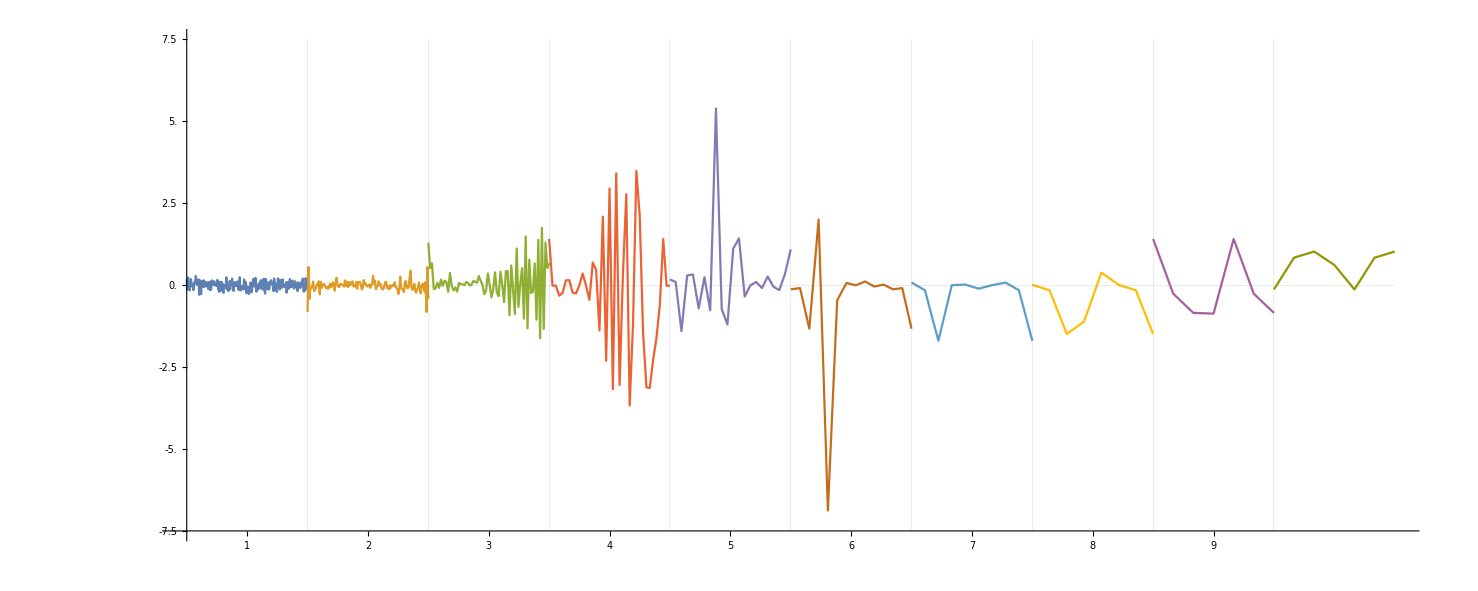

```mathematica
WaveletListPlot[DiscreteWaveletTransform[data,DaubechiesWavelet[4],9],PlotLayout->"CommonYAxis"]
```

```mathematica
data=Table[Sin[x^2],{x,0,10,0.02}];
```

```mathematica
dwd1=DiscreteWaveletTransform[data,DaubechiesWavelet[4],3]
dwd2=DiscreteWaveletTransform[data,SymletWavelet[4],3]
```

DiscreteWaveletData[<<DWT>>, <3>, {501}]

DiscreteWaveletData[<<DWT>>, <3>, {501}]

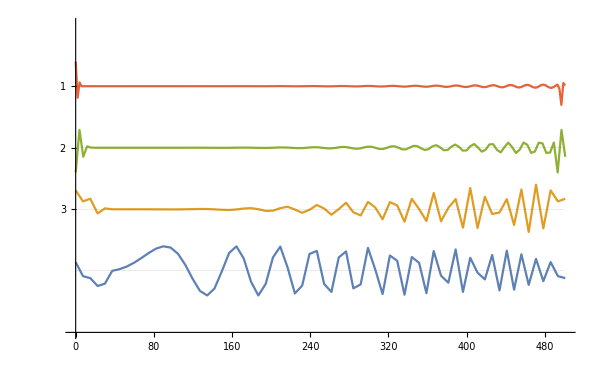
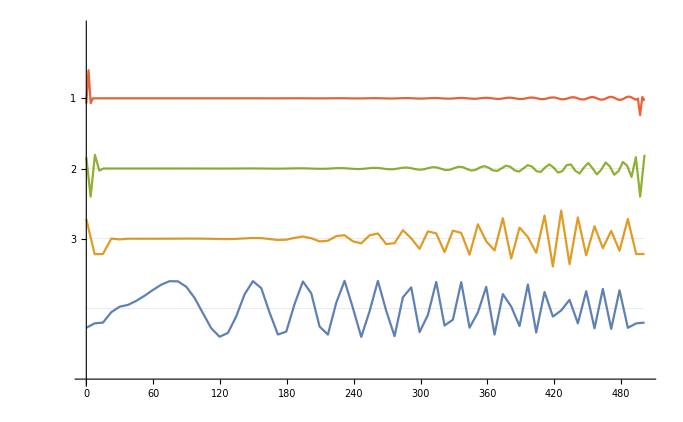

```mathematica
{WaveletListPlot[dwd1],WaveletListPlot[dwd2]}
```

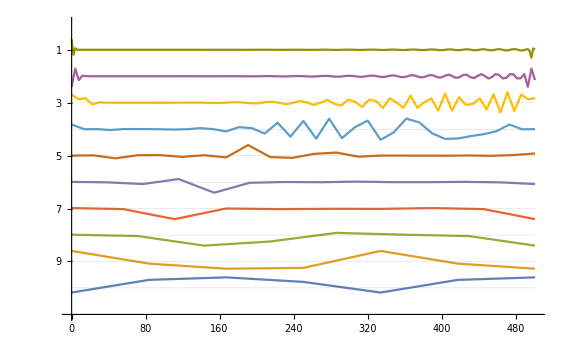
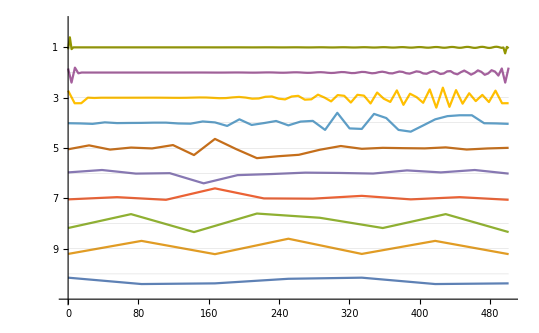

```mathematica
{WaveletListPlot[DiscreteWaveletTransform[data,DaubechiesWavelet[4],9]],WaveletListPlot[DiscreteWaveletTransform[data,SymletWavelet[4],9]]}
```

```mathematica
data=Table[Sin[t^2],{t,-3π,3π,0.01}];
```

```mathematica
dwd=DiscreteWaveletTransform[data,BattleLemarieWavelet[3],9]
```

DiscreteWaveletData[<<DWT>>, <9>, {1885}]

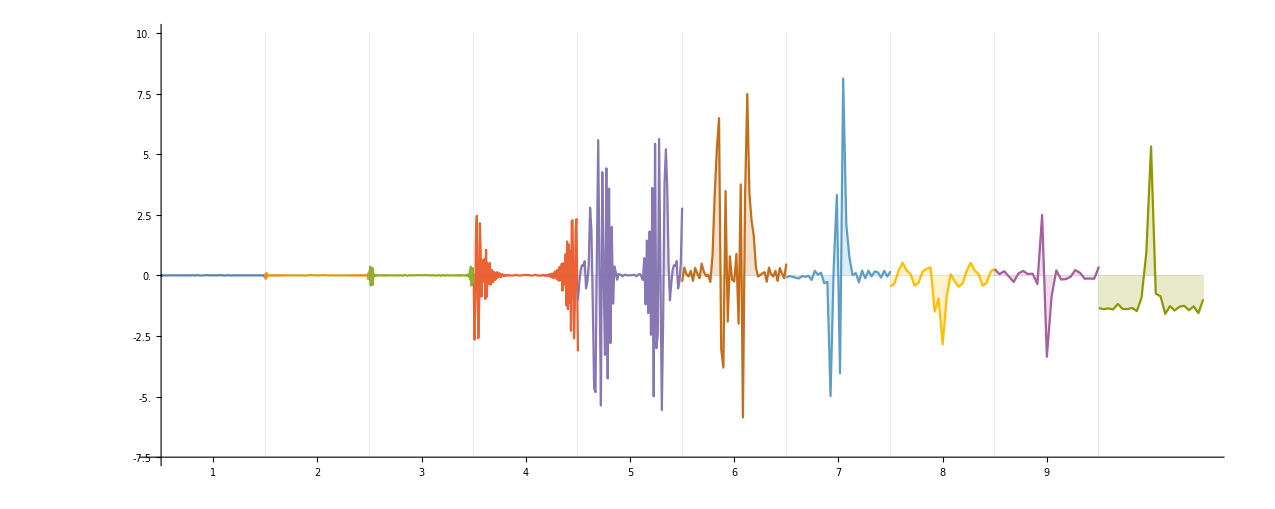

```mathematica
WaveletListPlot[dwd,PlotLayout->"CommonYAxis",Filling->Axis]
```

```mathematica
price = FinancialData["IBM","Jan. 1, 2000"]
```

TimeSeries[…]

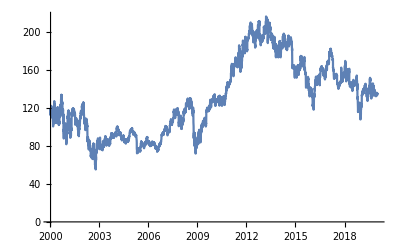

```mathematica
DateListPlot[price,Joined->True,Frame->False]
```

```mathematica
dwd = DiscreteWaveletTransform[price⟦All,2⟧,BiorthogonalSplineWavelet[3,3],4]
```

Part::partd: Part specification TemporalData[TimeSeries,{«1»},True,11.1]⟦All,2⟧ is longer than depth of object.

DiscreteWaveletTransform::wlist: Argument TemporalData[TimeSeries,{«1»},True,11.1]⟦All,2⟧ should be one of rectangular array of any depth, image, sound, or sampled sound list.

DiscreteWaveletTransform[TimeSeries[…]⟦All,2⟧,BiorthogonalSplineWavelet[3,3],4]

```mathematica
FinancialData["GE","Return",All]
```

{}